Hatano-Nelson-Kitaev Model: Monte Carlo Simulation |

The Modelpaclet:QuantumMob/QuantumPlaybook/tutorial/HatanoNelsonKitaevModel#503579431 | Simulation of the Projective Modelpaclet:QuantumMob/QuantumPlaybook/tutorial/HatanoNelsonKitaevModel#695511463
Simulation of the Dissipative Modelpaclet:QuantumMob/QuantumPlaybook/tutorial/HatanoNelsonKitaevModel#879704357 |

The Hatano-Nelson-Kitaev model is a generalization of the Hatano-Nelson model to include non-Hermitian anisotropic pairing potential.

BravyiStatepaclet:QuantumMob/Q3/ref/BravyiStateQuantumMob Package Symbol | Represents a fermionic Gaussian state.
BravyiNonunitarypaclet:QuantumMob/Q3/ref/BravyiNonunitaryQuantumMob Package Symbol | Represents a non-unitary evolution operator associated with local quadratic non-Hermitian Hamiltonian
BravyiJumppaclet:QuantumMob/Q3/ref/BravyiJumpQuantumMob Package Symbol | Represents a set of quantum jump operators
BravyiSimulatepaclet:QuantumMob/Q3/ref/BravyiSimulateQuantumMob Package Symbol | Simulates the quantum master equation for a dissipative fermionic system

Q3 functions for the Monte Carlo simulation of open quantum systems of non-interacting fermions.

Make sure to load the Q3 framework.

```mathematica
Needs["QuantumMob`Q3`"]
```

The Model

Consider a system of fermion modes.

```mathematica
$L=4;
```

```mathematica
Let[Fermion,f]
ff=f[Range@$L]
fff=Join[ff,Dagger@ff]
```

{f_(,,1),f_(,,2),f_(,,3),f_(,,4)}

{f_(,,1),f_(,,2),f_(,,3),f_(,,4),f_(,,1)^(,,†),f_(,,2)^(,,†),f_(,,3)^(,,†),f_(,,4)^(,,†)}

Here is the Hamiltonian for the Kitaev chain of Majorana modes.

```mathematica
Let[Real,μ,J,Δ,γ]
```

```mathematica
hamOp=μ*Q[ff]-(J/2)PlusDagger[Hop[ff]]+(Δ/2)PlusDagger[Pair[ff]]
```

-1/2 J (f_(,,1)^(,,†)f_(,,2)+f_(,,2)^(,,†)f_(,,1)+f_(,,2)^(,,†)f_(,,3)+f_(,,3)^(,,†)f_(,,2)+f_(,,3)^(,,†)f_(,,4)+f_(,,4)^(,,†)f_(,,3))+μ (f_(,,1)^(,,†)f_(,,1)+f_(,,2)^(,,†)f_(,,2)+f_(,,3)^(,,†)f_(,,3)+f_(,,4)^(,,†)f_(,,4))+1/2 Δ (-f_(,,1)^(,,†)f_(,,2)^(,,†)-f_(,,2)^(,,†)f_(,,3)^(,,†)-f_(,,3)^(,,†)f_(,,4)^(,,†)-f_(,,2)f_(,,1)-f_(,,3)f_(,,2)-f_(,,4)f_(,,3))

### Dissipative Model

Consider some auxiliary fermion modes to describe the quantum jump operators.

```mathematica
Let[Fermion,a,b]
aa=a[Range[$L-1]]
bb=b[Range[$L-1]]
```

{a_(,,1),a_(,,2),a_(,,3)}

{b_(,,1),b_(,,2),b_(,,3)}

Here are the quantum jump operators that are linear combinations of the fermion creation and annihilation operators.

```mathematica
a[k_]:=(f[k]+I*Dagger[f[k+1]])/Sqrt[2]
b[k_]:=(f[k]-I*Dagger[f[k+1]])/Sqrt[2]
ab=Join[aa,Dagger@bb];
ab//TableForm
```

(ⅈ f_(,,2)^(,,†)+f_(,,1))/(√2)
(ⅈ f_(,,3)^(,,†)+f_(,,2))/(√2)
(ⅈ f_(,,4)^(,,†)+f_(,,3))/(√2)
(f_(,,1)^(,,†)+ⅈ f_(,,2))/(√2)
(f_(,,2)^(,,†)+ⅈ f_(,,3))/(√2)
(f_(,,3)^(,,†)+ⅈ f_(,,4))/(√2)

In the fermionic quantum computation, these quantum jump operators are efficiently described by the coefficients matrix.

```mathematica
jmp=NambuCoefficients[ab,ff];
jmp//MatrixForm
```

(1/(√2) | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | 0 | ⅈ/(√2)
0 | ⅈ/(√2) | 0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | ⅈ/(√2) | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 1/(√2) | 0)

Construct the effective non-Hermitian Hamiltonian, which results in the so-called  Hatano-Nelson model.

```mathematica
dmpOp=γ*Total[Dagger[ab]**ab]/2//Garner
```

(3 γ)/2+1/2 ⅈ γ f_(,,1)^(,,†)f_(,,2)^(,,†)+1/2 ⅈ γ f_(,,2)^(,,†)f_(,,3)^(,,†)+1/2 ⅈ γ f_(,,3)^(,,†)f_(,,4)^(,,†)-1/2 ⅈ γ f_(,,2)f_(,,1)-1/2 ⅈ γ f_(,,3)f_(,,2)-1/2 ⅈ γ f_(,,4)f_(,,3)

```mathematica
gmm=dmpOp/.Thread[ff->0]
```

(3 γ)/2

```mathematica
dmp=NambuHermitian[2*CoefficientTensor[dmpOp,Dagger@fff,fff]]
```

NambuHermitian[…]

```mathematica
nonOp=hamOp-I*dmpOp//Garner
```

-(3 ⅈ γ)/2+1/2 (γ-Δ) f_(,,1)^(,,†)f_(,,2)^(,,†)+μ f_(,,1)^(,,†)f_(,,1)-1/2 J f_(,,1)^(,,†)f_(,,2)+1/2 (γ-Δ) f_(,,2)^(,,†)f_(,,3)^(,,†)-1/2 J f_(,,2)^(,,†)f_(,,1)+μ f_(,,2)^(,,†)f_(,,2)-1/2 J f_(,,2)^(,,†)f_(,,3)+1/2 (γ-Δ) f_(,,3)^(,,†)f_(,,4)^(,,†)-1/2 J f_(,,3)^(,,†)f_(,,2)+μ f_(,,3)^(,,†)f_(,,3)-1/2 J f_(,,3)^(,,†)f_(,,4)-1/2 J f_(,,4)^(,,†)f_(,,3)+μ f_(,,4)^(,,†)f_(,,4)+1/2 (-γ-Δ) f_(,,2)f_(,,1)+1/2 (-γ-Δ) f_(,,3)f_(,,2)+1/2 (-γ-Δ) f_(,,4)f_(,,3)

```mathematica
non=2*CoefficientTensor[nonOp,Dagger@fff,fff]//SimplifyThrough;
ArrayShort[-2non,"Size"->8]
```

(-2 μ | J | 0 | 0 | 0 | -γ+Δ | 0 | 0
J | -2 μ | J | 0 | γ-Δ | 0 | -γ+Δ | 0
0 | J | -2 μ | J | 0 | γ-Δ | 0 | -γ+Δ
0 | 0 | J | -2 μ | 0 | 0 | γ-Δ | 0
0 | -γ-Δ | 0 | 0 | 2 μ | -J | 0 | 0
γ+Δ | 0 | -γ-Δ | 0 | -J | 2 μ | -J | 0
0 | γ+Δ | 0 | -γ-Δ | 0 | -J | 2 μ | -J
0 | 0 | γ+Δ | 0 | 0 | 0 | -J | 2 μ)

```mathematica
altOp=MultiplyDot[Dagger@fff,non,fff]/2
altOp-nonOp//Garner
```

1/2 (-4 μ+(γ-Δ) f_(,,1)^(,,†)f_(,,2)^(,,†)+2 μ f_(,,1)^(,,†)f_(,,1)-J f_(,,1)^(,,†)f_(,,2)+(γ-Δ) f_(,,2)^(,,†)f_(,,3)^(,,†)-J f_(,,2)^(,,†)f_(,,1)+2 μ f_(,,2)^(,,†)f_(,,2)-J f_(,,2)^(,,†)f_(,,3)+(γ-Δ) f_(,,3)^(,,†)f_(,,4)^(,,†)-J f_(,,3)^(,,†)f_(,,2)+2 μ f_(,,3)^(,,†)f_(,,3)-J f_(,,3)^(,,†)f_(,,4)-J f_(,,4)^(,,†)f_(,,3)+2 μ f_(,,4)^(,,†)f_(,,4)+(-γ-Δ) f_(,,2)f_(,,1)+(-γ-Δ) f_(,,3)f_(,,2)+(-γ-Δ) f_(,,4)f_(,,3))

(3 ⅈ γ)/2-2 μ

In summary, the dissipative Hatano-Nelson-Kitaev (HNK) model can be written as

```mathematica
Clear[HNKDissipative]
HNKDissipative[{μ_,J_,Δ_},γ_,L_Integer]:=Module[
{hrm,del,ham,jmp},
hrm=-μ*One[L]-(J/2)*PlusTopple@One[{L,L},1];
del=-(Δ/2)*One[{L,L},1];
del=del-Transpose[del];
ham=NambuHermitian[{hrm,del}];
jmp={One[{L-1,L}],I*One[{L-1,L},1]};
jmp=ArrayFlatten@{jmp,Reverse@jmp};
jmp=Sqrt[γ]*Canonicalize[NambuJump@jmp];
{ham,jmp}
]
```

```mathematica
{ham,jmp}=HNKDissipative[{μ,J,Δ},γ,$L];
ArrayShort[ham,"Size"->6]
ArrayShort[jmp,"Size"->6]
```

{(-μ | -J/2 | 0 | 0
-J/2 | -μ | -J/2 | 0
0 | -J/2 | -μ | -J/2
0 | 0 | -J/2 | -μ),(0 | -Δ/2 | 0 | 0
Δ/2 | 0 | -Δ/2 | 0
0 | Δ/2 | 0 | -Δ/2
0 | 0 | Δ/2 | 0)}

{((√γ)/(√2) | 0 | 0 | 0
0 | (√γ)/(√2) | 0 | 0
0 | 0 | (√γ)/(√2) | 0
0 | (ⅈ √γ)/(√2) | 0 | 0
0 | 0 | (ⅈ √γ)/(√2) | 0
0 | 0 | 0 | (ⅈ √γ)/(√2)),(0 | (ⅈ √γ)/(√2) | 0 | 0
0 | 0 | (ⅈ √γ)/(√2) | 0
0 | 0 | 0 | (ⅈ √γ)/(√2)
(√γ)/(√2) | 0 | 0 | 0
0 | (√γ)/(√2) | 0 | 0
0 | 0 | (√γ)/(√2) | 0)}

```mathematica
{alt,tmp}=NambuDamping[jmp]
```

{NambuHermitian[…],(3 γ)/2}

```mathematica
alt-dmp//First//ArrayZeroQ
```

True

### Projective Model

Another choice of quantum jump operators that leads to the same Hatano-Nelson-Kitaev Hamiltonian is the projection operators L_(2k-1):=a_k^†a_k and L_(2k):=b_k b_k^†, where a_k and b_k are the auxiliary fermion modes defined above.

```mathematica
prj=Dagger[ab]**ab
```

{1/2+1/2 ⅈ f_(,,1)^(,,†)f_(,,2)^(,,†)+1/2 f_(,,1)^(,,†)f_(,,1)-1/2 f_(,,2)^(,,†)f_(,,2)-1/2 ⅈ f_(,,2)f_(,,1),1/2+1/2 ⅈ f_(,,2)^(,,†)f_(,,3)^(,,†)+1/2 f_(,,2)^(,,†)f_(,,2)-1/2 f_(,,3)^(,,†)f_(,,3)-1/2 ⅈ f_(,,3)f_(,,2),1/2+1/2 ⅈ f_(,,3)^(,,†)f_(,,4)^(,,†)+1/2 f_(,,3)^(,,†)f_(,,3)-1/2 f_(,,4)^(,,†)f_(,,4)-1/2 ⅈ f_(,,4)f_(,,3),1/2+1/2 ⅈ f_(,,1)^(,,†)f_(,,2)^(,,†)-1/2 f_(,,1)^(,,†)f_(,,1)+1/2 f_(,,2)^(,,†)f_(,,2)-1/2 ⅈ f_(,,2)f_(,,1),1/2+1/2 ⅈ f_(,,2)^(,,†)f_(,,3)^(,,†)-1/2 f_(,,2)^(,,†)f_(,,2)+1/2 f_(,,3)^(,,†)f_(,,3)-1/2 ⅈ f_(,,3)f_(,,2),1/2+1/2 ⅈ f_(,,3)^(,,†)f_(,,4)^(,,†)-1/2 f_(,,3)^(,,†)f_(,,3)+1/2 f_(,,4)^(,,†)f_(,,4)-1/2 ⅈ f_(,,4)f_(,,3)}

Since a_k^†a_k and b_k b_k^† are projection operators, it is clear that they reproduces the same effective damping operator; Σ_μ L_μ^†L_μ=Σ_k a_k^†a_k+Σ_k b_k^†b_k=2G.

```mathematica
dmpOp=γ*Total[prj]/2//Garner
```

(3 γ)/2+1/2 ⅈ γ f_(,,1)^(,,†)f_(,,2)^(,,†)+1/2 ⅈ γ f_(,,2)^(,,†)f_(,,3)^(,,†)+1/2 ⅈ γ f_(,,3)^(,,†)f_(,,4)^(,,†)-1/2 ⅈ γ f_(,,2)f_(,,1)-1/2 ⅈ γ f_(,,3)f_(,,2)-1/2 ⅈ γ f_(,,4)f_(,,3)

In summary, the projective Hatano-Nelson-Kitaev (HNK) model can be written as

```mathematica
Clear[HNKProjective]
HNKProjective[{μ_,J_,Δ_},γ_,L_Integer]:=Module[
{hrm,del,ham,msr},
hrm=-μ*One[L]-(J/2)*PlusTopple@One[{L,L},1];
del=-(Δ/2)*One[{L,L},1];
del=del-Transpose[del];
ham=NambuHermitian[{hrm,del}];
msr={One[{L-1,L}],I*One[{L-1,L},1]};
msr=ArrayFlatten@{msr,Reverse@msr};
msr=Surd[γ,4]*Canonicalize[NambuMeasurement@msr];
{ham,msr}
]
```

```mathematica
{ham,jmp}=HNKProjective[{μ,t,Δ},γ,$L];
ArrayShort[ham,"Size"->6]
ArrayShort[jmp,"Size"->6]
```

{(-μ | -t/2 | 0 | 0
-t/2 | -μ | -t/2 | 0
0 | -t/2 | -μ | -t/2
0 | 0 | -t/2 | -μ),(0 | -Δ/2 | 0 | 0
Δ/2 | 0 | -Δ/2 | 0
0 | Δ/2 | 0 | -Δ/2
0 | 0 | Δ/2 | 0)}

{(γ^(1/4)/(√2) | 0 | 0 | 0
0 | γ^(1/4)/(√2) | 0 | 0
0 | 0 | γ^(1/4)/(√2) | 0
0 | (ⅈ γ^(1/4))/(√2) | 0 | 0
0 | 0 | (ⅈ γ^(1/4))/(√2) | 0
0 | 0 | 0 | (ⅈ γ^(1/4))/(√2)),(0 | (ⅈ γ^(1/4))/(√2) | 0 | 0
0 | 0 | (ⅈ γ^(1/4))/(√2) | 0
0 | 0 | 0 | (ⅈ γ^(1/4))/(√2)
γ^(1/4)/(√2) | 0 | 0 | 0
0 | γ^(1/4)/(√2) | 0 | 0
0 | 0 | γ^(1/4)/(√2) | 0)}

```mathematica
{dmp,gmm}=NambuDamping[jmp]//Simplify[#,Assumptions->γ>0]&
```

{NambuHermitian[…],(3 γ)/2}

Simulation of the Dissipative Model

```mathematica
Needs["QuantumMob`Q3`"]
```

Set the number of fermion modes.

```mathematica
$L=6;
```

Set the parameters of the Hatano-Nelson-Kitaev model.

```mathematica
$μ=0.2;
$J=$Δ=1;
$γ=0.1;
```

Set the dissipative HNK model.

```mathematica
Clear[HNKDissipative]
HNKDissipative[{μ_,J_,Δ_},γ_,L_Integer]:=Module[
{hrm,del,ham,jmp},
hrm=-μ*One[L]-(J/2)*PlusTopple@One[{L,L},1];
del=-(Δ/2)*One[{L,L},1];
del=del-Transpose[del];
ham=NambuHermitian[{hrm,del}];
jmp={One[{L-1,L}],I*One[{L-1,L},1]};
jmp=ArrayFlatten@{jmp,Reverse@jmp};
jmp=Sqrt[γ]*Canonicalize[NambuJump@jmp];
{ham,jmp}
]
```

```mathematica
{ham,jmp}=HNKDissipative[{$μ,$J,$Δ},$γ,$L]
```

{NambuHermitian[…],NambuJump[…]}

Set the initial state.

```mathematica
in=BravyiState[{1,0},$L]
```

BravyiState[…]

Do the Monte Carlo simulation.

```mathematica
SeedRandom[381];
```

```mathematica
EchoTiming[
data=BravyiSimulate[in,ham,jmp,{$T=5,$dt=0.025},
"Samples"->100]
];
data//Dimensions
```

38.5286

{100,201}

Choose a subsystem.

```mathematica
sub=Range[$L/2]
```

{1,2,3}

Calculate the entanglement entropy (EE) between the subsystem and the rest.

```mathematica
EchoTiming[
ee=Re@Mean@BravyiEntanglementEntropy[data,sub]
];
```

1.11708

Check the entanglement entropy as a function of time.

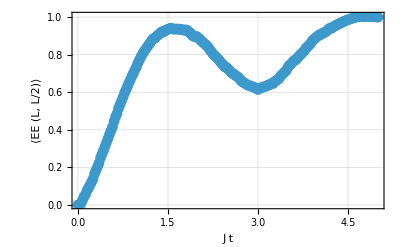

```mathematica
ListLinePlot[ee,
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"J t","⟨EE (L, L/2)⟩"}
]
```

Construct approximate density matrices by taking averages of the covariance matrices in different trajectories, and calculate the logarithmic negativity (LN) between the subsystem and the rest in the density matrices.

```mathematica
EchoTiming[
avg=BravyiMean[data];
negRho=Re@BravyiLogarithmicNegativity[avg,sub]
];
```

0.265961

Check the logarithmic negativity as a function of time.

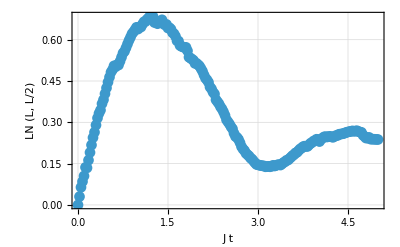

```mathematica
ListLinePlot[negRho,
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"J t","LN (L, L/2)"}
]
```

Simulation of the Projective Model

```mathematica
Needs["QuantumMob`Q3`"]
```

Set the number of fermion modes.

```mathematica
$L=6;
```

Set the parameters of the Hatano-Nelson-Kitaev model.

```mathematica
$μ=0.2;
$J=$Δ=1;
$γ=0.1;
```

Set the projective HNK model.

```mathematica
Clear[HNKProjective]
HNKProjective[{μ_,J_,Δ_},γ_,L_Integer]:=Module[
{hrm,del,ham,msr},
hrm=-μ*One[L]-(J/2)*PlusTopple@One[{L,L},1];
del=-(Δ/2)*One[{L,L},1];
del=del-Transpose[del];
ham=NambuHermitian[{hrm,del}];
msr={One[{L-1,L}],I*One[{L-1,L},1]};
msr=ArrayFlatten@{msr,Reverse@msr};
msr=Surd[γ,4]*Canonicalize[NambuMeasurement@msr];
{ham,msr}
]
```

```mathematica
{ham,msr}=HNKProjective[{$μ,$J,$Δ},$γ,$L]
```

{NambuHermitian[…],NambuMeasurement[…]}

Set the initial state.

```mathematica
in=BravyiState[{1,0},$L]
```

BravyiState[…]

Do the Monte Carlo simulation.

```mathematica
SeedRandom[381];
```

```mathematica
EchoTiming[
data=BravyiSimulate[in,ham,msr,{$T=5,$dt=0.025},
"Samples"->100]
];
data//Dimensions
```

38.3392

{100,201}

Choose a subsystem.

```mathematica
sub=Range[$L/2]
```

{1,2,3}

Calculate the entanglement entropy (EE) between the subsystem and the rest.

```mathematica
EchoTiming[
ee=Re@Mean@BravyiEntanglementEntropy[data,sub]
];
```

1.13801

Check the entanglement entropy as a function of time.

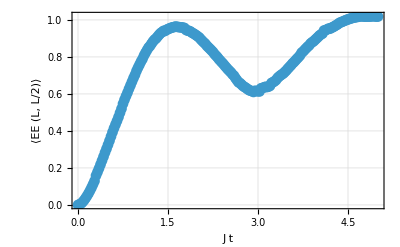

```mathematica
ListLinePlot[ee,
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"J t","⟨EE (L, L/2)⟩"}
]
```

Construct approximate density matrices by taking averages of the covariance matrices in different trajectories, and calculate the logarithmic negativity (LN) between the subsystem and the rest in the density matrices.

```mathematica
EchoTiming[
avg=BravyiMean[data];
negRho=Re@BravyiLogarithmicNegativity[avg,sub]
];
```

0.263145

Check the logarithmic negativity as a function of time.

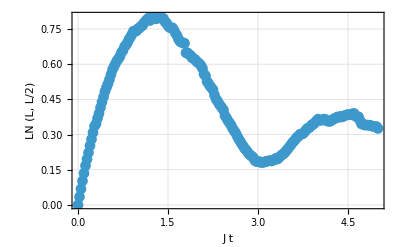

```mathematica
ListLinePlot[negRho,
DataRange->{0,$T},
PlotRange->All,
PlotMarkers->Automatic,
FrameLabel->{"J t","LN (L, L/2)"}
]
```

| Related Guides
▪Fermionic Quantum Computation
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪Majorana Fermions
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start

| Related Links
▪A. Yu. Kitaev (2001)https://doi.org/10.1070/1063-7869/44/10S/S29, Physics-Uspekhi 44, 131 (2001), "Unpaired Majorana fermions in quantum wires." 
▪K. Kawabata, T. https://doi.org/10.1103/PhysRevX.13.021007Numasawahttps://doi.org/10.1103/PhysRevX.13.021007 and S. Ryu (2023)https://doi.org/10.1103/PhysRevX.13.021007, Physical Review X 13, 021007, "Entanglement Phase Transition Induced by the Non-Hermitian Skin Effect."
▪X. https://doi.org/10.1103/PhysRevB.110.144305Feng and S. Chen (2024)https://doi.org/10.1103/PhysRevB.110.144305, Physical Review B 110, 144305, "Delocalization of skin steady states."
▪N. https://doi.org/10.1103/PhysRevLett.77.570Hatano and D. R. Nelson (1996)https://doi.org/10.1103/PhysRevLett.77.570, Physical Review Letters 77, 570, "Localization Transitions in Non-Hermitian Quantum Mechanics."
▪N. https://doi.org/10.1103/PhysRevB.56.8651Hatano and D. R. Nelson (1997)https://doi.org/10.1103/PhysRevB.56.8651, Physical Review B 56, 287, "Vortex Pinning and Non-Hermitian Quantum Mechanics."
▪Mahnhttps://doi.org/10.1007/978-3-030-91214-7-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).